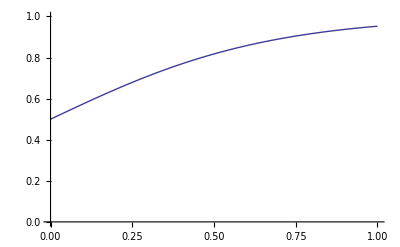

```mathematica
(* Traditional sigmoidal function  and its graphs*)
f1[a_,b_,x_]=1/(ⅇ^(-(a x)-b)+1);
Plot[f1[3,0,x],{x,0,1},PlotRange->{0,1}]
Manipulate[Plot[f1[a,b,x],{x,0,1},PlotRange->{0,1}],{a,-100,100,0.1},{b,-40,0,0.1}]
```

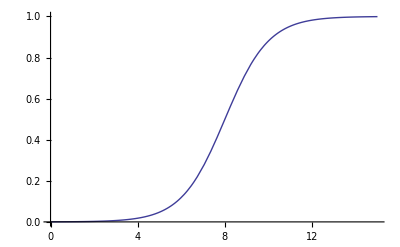

```mathematica
(* Main sigmoidal function that we are implementing and its graphs *)
Clear["Global`*"]
f2[A_,Ka_,B_,M_,x_]=A+(Ka-A)/(1+ⅇ^(-B*(x-M)));
Plot[f2[0,1,1,8,x],{x,0,15},PlotRange->{0,1}]
Manipulate[
Plot[f2[A,Ka,B,M,x],{x,0,15},PlotRange->{0,1}],
{{A,0},-10,10,.01},
{{Ka,1},-10,10,.01},
{{B,1},-10,10,.01},
{{M,8},7.5-20,7.5+20,.01}]
```

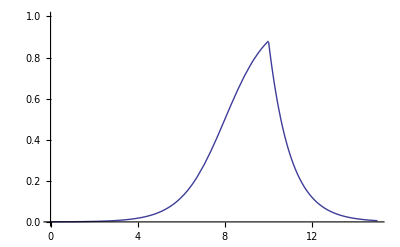

```mathematica
(* Combination of standart sigmoidal function with an exponential decay. 
   They ate combined with Unit Step Function. It is extremely slow in R computations *)
Clear["Global`*"]
f3[A_,Ka_,B_,M_,P_,alf_,x_]=(1-UnitStep[x-P])*(A+(Ka-A)/(1+ⅇ^(-B*(x-M))))+UnitStep[x-P]*(A+(Ka-A)/(1+ⅇ^(-B*(P-M))))*ⅇ^(-alf*x)/ⅇ^(-alf*P);
Plot[f3[0,1,1,8,10,1,x],{x,0,15},PlotRange->{0,1}]
Manipulate[
Plot[f3[A,Ka,B,M,P,alf,x],{x,0,15},PlotRange->{0,1}],
{{A,0},-10,10,.01},
{{Ka,1},-10,10,.01},
{{B,1},-10,10,.01},
{{M,8},7.5-20,7.5+20,.01},
{{P,10},0,15,0.01},
{{alf,1},1/100,10,0.001}]
```

A1 Ka

A2 Ka

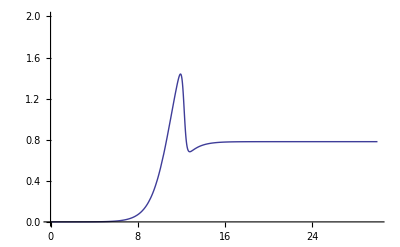

```mathematica
(* Current double sigmodal function that we are using. 
An example problematic case is shown; tha case is coming from original data set. MOI<-"500", Cell<-36, Group<-"HR". Note in the original function A1 is not a variable but fixed to 0*)

Clear["Global`*"]
f4[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=(A1+(Ka-A1)/(1+ⅇ^(-B1*(x-M1))))*(A2+(Ka-A2)/(1+ⅇ^(B2*(x-(M1+L)))));
$Assumptions={B1>0&&B2>0&&L>0};
Limit[f4[A1,A2,Ka,B1,M1,B2,L,x],x->-∞,Assumptions->{B1>0,B2>0,L>0}]
Limit[f4[A1,A2,Ka,B1,M1,B2,L,x],x->∞,Assumptions->{B1>0,B2>0,L>0}]

Plot[f4[0,0.5368628,1.454867,1.084971,11.11337,8.529749,1.13329,x],{x,0,30},PlotRange->{0,2}]
Manipulate[
Plot[f4[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},PlotRange->{0,2}],
{{A1,0},0,1,.01},
{{A2,0.5368628},0,1,.01},
{{Ka,1.454867},0,2,.01},
{{B1,1.084971},0,10,.01},
{{M1,11.11337},0,20,.01},
{{B2,8.529749},0,10,0.01},
{{L,1.13329},0,10,0.001}]
```

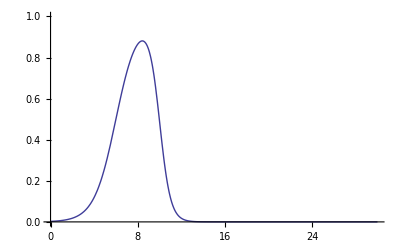

```mathematica
(* A single function that has same minimum on both ends but variable slopes for increase and decrease. *)
Clear["Global`*"]
f5a[A_,Ka_,B1_,M1_,B2_,L_,x_]=A+((Ka-A)/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L))))));
Plot[f5a[0,1,1,6,2,4,x],{x,0,30},PlotRange->{0,1}]
Manipulate[
Plot[f5a[A,Ka,B1,M1,B2,L,x],{x,0,30},PlotRange->{0,1}],
{{A,0},0,1,.01},
{{Ka,1},0,1,.01},
{{B1,1},0,10,.01},
{{M1,6},7.5-20,7.5+20,.01},
{{B2,2},0,10,0.01},
{{L,10},0,10,0.001}]
```

```mathematica
(* Candidate function both includes; central symmetric model in f5a & 2 unnormalized side functions that describe the initial and final heights.
The model fails when A1 and A2 are bigger than Ka
*)
Clear["Global`*"]
f5b[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=(Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L))))))+(A2/(1+ⅇ^(-B2*(x-(M1+L)))))+(A1/(1+ⅇ^(B1*(x-M1))));

$Assumptions={B1>0&&B2>0&&L>0};
Limit[f5b[A1,A2,Ka,B1,M1,B2,L,x],x->-∞,Assumptions->{B1>0,B2>0,L>0}]
Limit[f5b[A1,A2,Ka,B1,M1,B2,L,x],x->∞,Assumptions->{B1>0,B2>0,L>0}]
Solve[D[f5b[A1,A2,Ka,B1,M1,B2,L,x],x]==0,x]
Expand[f5b[A1,A2,Ka,B1,M1,B2,L,x]]

Plot[f5b[0,0,1,1,6,2,4,x],{x,0,30},PlotRange->{0,1}]
Manipulate[
Plot[f5b[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},PlotRange->{0,1}],
{{A1,0},0,1,.01},
{{A2,0},0,1,.01},
{{Ka,1},0,1,.01},
{{B1,1},0.01,10,.01},
{{M1,6},7.5-20,7.5+20,.01},
{{B2,2},0.01,10,0.01},
{{L,10},0,10,0.001}]
```

A1

A2

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[-(A1 B1 ⅇ^(B1 (-M1+x)))/((1+ⅇ^(B1 (-M1+x)))^2)+(A2 B2 ⅇ^(-B2 (-L-M1+x)))/((1+ⅇ^(-B2 (-L-M1+x)))^2)-(B2 ⅇ^(B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)+(B1 ⅇ^(-B1 (-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))==0,x]

A1/(1+ⅇ^(B1 (-M1+x)))+A2/(1+ⅇ^(-B2 (-L-M1+x)))+Ka/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x))))

-Graphics-

```mathematica
(* Properly normalized candidate model with no fixed side. A1 and A2 can change between 0-1 and represents the heights of right and left arm wrt central part *)
Clear["Global`*"]
f5c[A1_,A2_,Ka_,B1_,M1_,B2_,L_,x_]=(Ka/((1+ⅇ^(-B1*(x-M1)))*(1+ⅇ^(B2*(x-(M1+L))))))+((Ka*A2)/(1+ⅇ^(-B2*(x-(M1+L)))))+((Ka*A1)/(1+ⅇ^(B1*(x-M1))));

$Assumptions={B1>0&&B2>0&&L>0};
Limit[f5c[A1,A2,Ka,B1,M1,B2,L,x],x->-∞,Assumptions->{B1>0,B2>0,L>0}]
Limit[f5c[A1,A2,Ka,B1,M1,B2,L,x],x->∞,Assumptions->{B1>0,B2>0,L>0}]
Solve[D[f5c[A1,A2,Ka,B1,M1,B2,L,x],x]==0,x]

Plot[f5c[0,0,1,1,6,2,4,x],{x,0,30},PlotRange->{0,1}]
Manipulate[
Plot[f5c[A1,A2,Ka,B1,M1,B2,L,x],{x,0,30},PlotRange->{0,1}],
{{A1,0},0,1,.01},
{{A2,0},0,1,.01},
{{Ka,1},0,1,.01},
{{B1,1},0.01,10,.01},
{{M1,6},7.5-20,7.5+20,.01},
{{B2,2},0.01,10,0.01},
{{L,10},0,10,0.001}]
```

A1 Ka

A2 Ka

Solve::tdep: The equations appear to involve the variables to be solved for in an essentially non-algebraic way.

Solve[-(A1 B1 ⅇ^(B1 (-M1+x)) Ka)/((1+ⅇ^(B1 (-M1+x)))^2)+(A2 B2 ⅇ^(-B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B2 (-L-M1+x)))^2)-(B2 ⅇ^(B2 (-L-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x))) (1+ⅇ^(B2 (-L-M1+x)))^2)+(B1 ⅇ^(-B1 (-M1+x)) Ka)/((1+ⅇ^(-B1 (-M1+x)))^2 (1+ⅇ^(B2 (-L-M1+x))))==0,x]

-Graphics-